```mathematica
FilterSymbol[sym_,vertices_]:=Block[{v2=SymbolToSets[sym]},
v2=Map[Select[#,MemberQ[vertices,#]&]&,v2];
v2=Select[v2,#≠{}&];
v2=Sort[Map[Sort[#]&,v2],#1[[1]]<#2[[1]]&];
Simplify[SetsToSymbol[v2]]
]
```

```mathematica
FilterSymbol[v156x2x34,Range[5]]
```

v15x2x34

```mathematica
FindPos[list_,exp_]:=Block[{pos},
For[pos=1,pos≤ Length[list],pos++,
If[exp[list[[pos]]], Return[pos]]
]
]
```

```mathematica
ReduceSymbol[value_]:=Block[{sets,pos,mult=1,le},
If[!PlanarGraphQ[value["graph"]],
0
,
sets=SymbolToSets[value["colofour"]];
pos=FindPos [sets,MemberQ[#,6]&];
le=Length[sets[[pos]]];
If[le==1,
mult=x-Length[sets]+1
,
mult=1
];
mult*FilterSymbol[value["colofour"],Range[5]]
]
]
```

```mathematica
Tally[Table[ReduceSymbol[allGraphs5[k]],{k,allGraphs5AtomKeys}]]
```

Part::pkspec1: The expression Null cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{0,1},{v1x2x3x45,1},{v1x2x35x4,1},{v1x2x34x5,1},{v1x2x345,1},{v1x25x3x4,1},{v1x25x34,1},{v1x24x3x5,1},{v1x24x35,1},{v1x245x3,1},{v1x23x4x5,1},{v1x23x45,1},{v1x235x4,1},{v1x234x5,1},{v1x2345,1},{v15x2x3x4,1},{v15x2x34,1},{v15x24x3,1},{v15x23x4,1},{v15x234,1},{v14x2x3x5,1},{v14x2x35,1},{v14x25x3,1},{v14x23x5,1},{v14x235,1},{v145x2x3,1},{v145x23,1},{v13x2x4x5,1},{v13x2x45,1},{v13x25x4,1},{v13x24x5,1},{v13x245,1},{v135x2x4,1},{v135x24,1},{v134x2x5,1},{v134x25,1},{v1345x2,1},{v12x3x4x5,1},{v12x3x45,1},{v12x35x4,1},{v12x34x5,1},{v12x345,1},{v125x3x4,1},{v125x34,1},{v124x3x5,1},{v124x35,1},{v1245x3,1},{v123x4x5,1},{v123x45,1},{v1235x4,1},{v1234x5,1},{v12345,1}}

```mathematica
Tally[Table[ReduceSymbol[allGraphs6[k]],{k,allGraphs6AtomKeys}]]
```

{{0,16},{v1x2x3x45,4},{v1x2x35x4,4},{v1x2x34x5,4},{v1x2x345 (-3+x),1},{v1x2x345,3},{v1x25x3x4,4},{v1x25x34 (-3+x),1},{v1x25x34,3},{v1x24x3x5,4},{v1x24x35 (-3+x),1},{v1x24x35,3},{v1x245x3 (-3+x),1},{v1x245x3,3},{v1x23x4x5,4},{v1x23x45 (-3+x),1},{v1x23x45,3},{v1x235x4 (-3+x),1},{v1x235x4,3},{v1x234x5 (-3+x),1},{v1x234x5,3},{v1x2345 (-2+x),1},{v1x2345,2},{v15x2x3x4,4},{v15x2x34 (-3+x),1},{v15x2x34,3},{v15x24x3 (-3+x),1},{v15x24x3,3},{v15x23x4 (-3+x),1},{v15x23x4,3},{v15x234 (-2+x),1},{v15x234,2},{v14x2x3x5,4},{v14x2x35 (-3+x),1},{v14x2x35,3},{v14x25x3 (-3+x),1},{v14x25x3,3},{v14x23x5 (-3+x),1},{v14x23x5,3},{v14x235 (-2+x),1},{v14x235,2},{v145x2x3 (-3+x),1},{v145x2x3,3},{v145x23 (-2+x),1},{v145x23,2},{v13x2x4x5,4},{v13x2x45 (-3+x),1},{v13x2x45,3},{v13x25x4 (-3+x),1},{v13x25x4,3},{v13x24x5 (-3+x),1},{v13x24x5,3},{v13x245 (-2+x),1},{v13x245,2},{v135x2x4 (-3+x),1},{v135x2x4,3},{v135x24 (-2+x),1},{v135x24,2},{v134x2x5 (-3+x),1},{v134x2x5,3},{v134x25 (-2+x),1},{v134x25,2},{v1345x2 (-2+x),1},{v1345x2,2},{v12x3x4x5,4},{v12x3x45 (-3+x),1},{v12x3x45,3},{v12x35x4 (-3+x),1},{v12x35x4,3},{v12x34x5 (-3+x),1},{v12x34x5,3},{v12x345 (-2+x),1},{v12x345,2},{v125x3x4 (-3+x),1},{v125x3x4,3},{v125x34 (-2+x),1},{v125x34,2},{v124x3x5 (-3+x),1},{v124x3x5,3},{v124x35 (-2+x),1},{v124x35,2},{v1245x3 (-2+x),1},{v1245x3,2},{v123x4x5 (-3+x),1},{v123x4x5,3},{v123x45 (-2+x),1},{v123x45,2},{v1235x4 (-2+x),1},{v1235x4,2},{v1234x5 (-2+x),1},{v1234x5,2},{v12345 (-1+x),1},{v12345,1}}

```mathematica
repSix2Five=Table[allGraphs6[k,"colofour"]->ReduceSymbol[allGraphs6[k]],{k,allGraphs6AtomKeys}]
```

{v1x2x3x4x5x6→0,v1x2x3x4x56→0,v1x2x3x46x5→0,v1x2x3x45x6→0,v1x2x3x456→v1x2x3x45,v1x2x36x4x5→0,v1x2x36x45→v1x2x3x45,v1x2x35x4x6→0,v1x2x35x46→v1x2x35x4,v1x2x356x4→v1x2x35x4,v1x2x34x5x6→0,v1x2x34x56→v1x2x34x5,v1x2x346x5→v1x2x34x5,v1x2x345x6→v1x2x345 (-3+x),v1x2x3456→v1x2x345,v1x26x3x4x5→0,v1x26x3x45→v1x2x3x45,v1x26x35x4→v1x2x35x4,v1x26x34x5→v1x2x34x5,v1x26x345→v1x2x345,v1x25x3x4x6→0,v1x25x3x46→v1x25x3x4,v1x25x36x4→v1x25x3x4,v1x25x34x6→v1x25x34 (-3+x),v1x25x346→v1x25x34,v1x256x3x4→v1x25x3x4,v1x256x34→v1x25x34,v1x24x3x5x6→0,v1x24x3x56→v1x24x3x5,v1x24x36x5→v1x24x3x5,v1x24x35x6→v1x24x35 (-3+x),v1x24x356→v1x24x35,v1x246x3x5→v1x24x3x5,v1x246x35→v1x24x35,v1x245x3x6→v1x245x3 (-3+x),v1x245x36→v1x245x3,v1x2456x3→v1x245x3,v1x23x4x5x6→0,v1x23x4x56→v1x23x4x5,v1x23x46x5→v1x23x4x5,v1x23x45x6→v1x23x45 (-3+x),v1x23x456→v1x23x45,v1x236x4x5→v1x23x4x5,v1x236x45→v1x23x45,v1x235x4x6→v1x235x4 (-3+x),v1x235x46→v1x235x4,v1x2356x4→v1x235x4,v1x234x5x6→v1x234x5 (-3+x),v1x234x56→v1x234x5,v1x2346x5→v1x234x5,v1x2345x6→v1x2345 (-2+x),v1x23456→v1x2345,v16x2x3x4x5→0,v16x2x3x45→v1x2x3x45,v16x2x35x4→v1x2x35x4,v16x2x34x5→v1x2x34x5,v16x2x345→v1x2x345,v16x25x3x4→v1x25x3x4,v16x25x34→v1x25x34,v16x24x3x5→v1x24x3x5,v16x24x35→v1x24x35,v16x245x3→v1x245x3,v16x23x4x5→v1x23x4x5,v16x23x45→v1x23x45,v16x235x4→v1x235x4,v16x234x5→v1x234x5,v16x2345→v1x2345,v15x2x3x4x6→0,v15x2x3x46→v15x2x3x4,v15x2x36x4→v15x2x3x4,v15x2x34x6→v15x2x34 (-3+x),v15x2x346→v15x2x34,v15x26x3x4→v15x2x3x4,v15x26x34→v15x2x34,v15x24x3x6→v15x24x3 (-3+x),v15x24x36→v15x24x3,v15x246x3→v15x24x3,v15x23x4x6→v15x23x4 (-3+x),v15x23x46→v15x23x4,v15x236x4→v15x23x4,v15x234x6→v15x234 (-2+x),v15x2346→v15x234,v156x2x3x4→v15x2x3x4,v156x2x34→v15x2x34,v156x24x3→v15x24x3,v156x23x4→v15x23x4,v156x234→v15x234,v14x2x3x5x6→0,v14x2x3x56→v14x2x3x5,v14x2x36x5→v14x2x3x5,v14x2x35x6→v14x2x35 (-3+x),v14x2x356→v14x2x35,v14x26x3x5→v14x2x3x5,v14x26x35→v14x2x35,v14x25x3x6→v14x25x3 (-3+x),v14x25x36→v14x25x3,v14x256x3→v14x25x3,v14x23x5x6→v14x23x5 (-3+x),v14x23x56→v14x23x5,v14x236x5→v14x23x5,v14x235x6→v14x235 (-2+x),v14x2356→v14x235,v146x2x3x5→v14x2x3x5,v146x2x35→v14x2x35,v146x25x3→v14x25x3,v146x23x5→v14x23x5,v146x235→v14x235,v145x2x3x6→v145x2x3 (-3+x),v145x2x36→v145x2x3,v145x26x3→v145x2x3,v145x23x6→v145x23 (-2+x),v145x236→v145x23,v1456x2x3→v145x2x3,v1456x23→v145x23,v13x2x4x5x6→0,v13x2x4x56→v13x2x4x5,v13x2x46x5→v13x2x4x5,v13x2x45x6→v13x2x45 (-3+x),v13x2x456→v13x2x45,v13x26x4x5→v13x2x4x5,v13x26x45→v13x2x45,v13x25x4x6→v13x25x4 (-3+x),v13x25x46→v13x25x4,v13x256x4→v13x25x4,v13x24x5x6→v13x24x5 (-3+x),v13x24x56→v13x24x5,v13x246x5→v13x24x5,v13x245x6→v13x245 (-2+x),v13x2456→v13x245,v136x2x4x5→v13x2x4x5,v136x2x45→v13x2x45,v136x25x4→v13x25x4,v136x24x5→v13x24x5,v136x245→v13x245,v135x2x4x6→v135x2x4 (-3+x),v135x2x46→v135x2x4,v135x26x4→v135x2x4,v135x24x6→v135x24 (-2+x),v135x246→v135x24,v1356x2x4→v135x2x4,v1356x24→v135x24,v134x2x5x6→v134x2x5 (-3+x),v134x2x56→v134x2x5,v134x26x5→v134x2x5,v134x25x6→v134x25 (-2+x),v134x256→v134x25,v1346x2x5→v134x2x5,v1346x25→v134x25,v1345x2x6→v1345x2 (-2+x),v1345x26→v1345x2,v13456x2→v1345x2,v12x3x4x5x6→0,v12x3x4x56→v12x3x4x5,v12x3x46x5→v12x3x4x5,v12x3x45x6→v12x3x45 (-3+x),v12x3x456→v12x3x45,v12x36x4x5→v12x3x4x5,v12x36x45→v12x3x45,v12x35x4x6→v12x35x4 (-3+x),v12x35x46→v12x35x4,v12x356x4→v12x35x4,v12x34x5x6→v12x34x5 (-3+x),v12x34x56→v12x34x5,v12x346x5→v12x34x5,v12x345x6→v12x345 (-2+x),v12x3456→v12x345,v126x3x4x5→v12x3x4x5,v126x3x45→v12x3x45,v126x35x4→v12x35x4,v126x34x5→v12x34x5,v126x345→v12x345,v125x3x4x6→v125x3x4 (-3+x),v125x3x46→v125x3x4,v125x36x4→v125x3x4,v125x34x6→v125x34 (-2+x),v125x346→v125x34,v1256x3x4→v125x3x4,v1256x34→v125x34,v124x3x5x6→v124x3x5 (-3+x),v124x3x56→v124x3x5,v124x36x5→v124x3x5,v124x35x6→v124x35 (-2+x),v124x356→v124x35,v1246x3x5→v124x3x5,v1246x35→v124x35,v1245x3x6→v1245x3 (-2+x),v1245x36→v1245x3,v12456x3→v1245x3,v123x4x5x6→v123x4x5 (-3+x),v123x4x56→v123x4x5,v123x46x5→v123x4x5,v123x45x6→v123x45 (-2+x),v123x456→v123x45,v1236x4x5→v123x4x5,v1236x45→v123x45,v1235x4x6→v1235x4 (-2+x),v1235x46→v1235x4,v12356x4→v1235x4,v1234x5x6→v1234x5 (-2+x),v1234x56→v1234x5,v12346x5→v1234x5,v12345x6→v12345 (-1+x),v123456→v12345}

```mathematica
Select[Keys[allGraphs6],IsomorphicGraphQ[WheelGraph[6],allGraphs6[#,"graph"]]&]
```

{7171258,7171210,7167046,7166838,7165594,7165434,7153948,7153788,7152544,7152336,7148172,7148124,6937978,6937930,6930958,6929506,6917764,6916360,6583846,6583638,6581038,6575214,6563308,6557692,6465754,6465594,6462946,6458574,6443752,6439540,5520988,5520828,5518084,5513548,5499210,5494834,5402944,5402736,5400040,5393992,5382570,5376730,5048652,5048604,5041372,5039860,5028274,5026810,2330236,2330140,2325864,2325604,2312670,2312506,2213596,2213500,2207772,2207452,2194626,2194402,1859304,1859044,1857852,1857532,1840330,1840270,796350,796186,794946,794722,790570,790510}

```mathematica
allGraphs6[7171258,"graph"]
```

-Graphics-

```mathematica
Table[ShowGraph6Least[k]->((allGraphs6[k,"colofour"]/.repSix2Five)/.RepGraph["C"]), {k,Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&&VertexDegree[allGraphs6[#,"graph"],6]==5&&IsomorphicGraphQ[WheelGraph[6],allGraphs6[#,"graph"]]&&allGraphs6[#,"comp"]===Greater&]}]
```

{}

```mathematica
ChromaticPolynomial[-Graphics-,4]
```

120

```mathematica
ChromaticPolynomial[-Graphics-,4]
```

24

```mathematica
ChromaticPolynomial[-Graphics-,4]
```

```mathematica
7*24
```

168

```mathematica
Table[ShowGraph6Least[k,"comp"]->CoefficientList[((allGraphs6[k,"colofour"]/.repSix2Five)),x]/.RepGraph["C"], {k,Select[Keys[allGraphs6],IsomorphicGraphQ[WheelGraph[6],allGraphs6[#,"graph"]]&]}]
```

{-Graphics-7171258GreaterEqual→{-3 -Graphics-295600+-Graphics-295330+-Graphics-295510+2 -Graphics-295250,-Graphics-295600},-Graphics-7171210GreaterEqual→{-3 -Graphics-295600+-Graphics-295330+-Graphics-295510+2 -Graphics-295270,-Graphics-295600},-Graphics-7167046GreaterEqual→{-3 -Graphics-296080+-Graphics-296050+2 -Graphics-295250+-Graphics-295270,-Graphics-296080},-Graphics-7166838GreaterEqual→{-3 -Graphics-296080+-Graphics-296050+2 -Graphics-295330+-Graphics-295270,-Graphics-296080},-Graphics-7165594GreaterEqual→{-3 -Graphics-296080+-Graphics-296050+2 -Graphics-295510+-Graphics-295270,-Graphics-296080},-Graphics-7165434GreaterEqual→{-3 -Graphics-295600+2 -Graphics-296050+-Graphics-295330+-Graphics-295510,-Graphics-295600},-Graphics-7153948GreaterEqual→{-3 -Graphics-297681+-Graphics-297670+-Graphics-295250+2 -Graphics-295270,-Graphics-297681},-Graphics-7153788GreaterEqual→{-3 -Graphics-297681+-Graphics-297670+2 -Graphics-295330+-Graphics-295250,-Graphics-297681},-Graphics-7152544GreaterEqual→{-3 -Graphics-297681+-Graphics-297670+2 -Graphics-295510+-Graphics-295250,-Graphics-297681},-Graphics-7152336GreaterEqual→{-3 -Graphics-295600+2 -Graphics-297670+-Graphics-295330+-Graphics-295510,-Graphics-295600},-Graphics-7148172GreaterEqual→{-3 -Graphics-297681+-Graphics-297670+2 -Graphics-296050+-Graphics-295250,-Graphics-297681},-Graphics-7148124GreaterEqual→{-3 -Graphics-296080+2 -Graphics-297670+-Graphics-296050+-Graphics-295270,-Graphics-296080},-Graphics-6937978GreaterEqual→{-3 -Graphics-302621+-Graphics-295330+-Graphics-302530+2 -Graphics-295250,-Graphics-302621},-Graphics-6937930GreaterEqual→{-3 -Graphics-302621+-Graphics-295330+-Graphics-302530+2 -Graphics-295270,-Graphics-302621},-Graphics-6930958GreaterEqual→{-3 -Graphics-303340+-Graphics-296050+-Graphics-302530+2 -Graphics-295250,-Graphics-303340},-Graphics-6929506GreaterEqual→{-3 -Graphics-303340+-Graphics-296050+-Graphics-302530+2 -Graphics-295510,-Graphics-303340},-Graphics-6917764GreaterEqual→{-3 -Graphics-304961+-Graphics-297670+-Graphics-302530+2 -Graphics-295270,-Graphics-304961},-Graphics-6916360GreaterEqual→{-3 -Graphics-304961+-Graphics-297670+-Graphics-302530+2 -Graphics-295510,-Graphics-304961},-Graphics-6583846GreaterEqual→{-3 -Graphics-317140+-Graphics-317110+2 -Graphics-295250+-Graphics-295270,-Graphics-317140},-Graphics-6583638GreaterEqual→{-3 -Graphics-317140+-Graphics-317110+2 -Graphics-295330+-Graphics-295270,-Graphics-317140},-Graphics-6581038GreaterEqual→{-3 -Graphics-317380+-Graphics-317110+-Graphics-295510+2 -Graphics-295250,-Graphics-317380},-Graphics-6575214GreaterEqual→{-3 -Graphics-317380+-Graphics-317110+2 -Graphics-296050+-Graphics-295510,-Graphics-317380},-Graphics-6563308GreaterEqual→{-3 -Graphics-319540+-Graphics-297670+-Graphics-317110+2 -Graphics-295330,-Graphics-319540},-Graphics-6557692GreaterEqual→{-3 -Graphics-319540+-Graphics-297670+-Graphics-317110+2 -Graphics-296050,-Graphics-319540},-Graphics-6465754GreaterEqual→{-3 -Graphics-317140+-Graphics-317110+2 -Graphics-302530+-Graphics-295270,-Graphics-317140},-Graphics-6465594GreaterEqual→{-3 -Graphics-302621+2 -Graphics-317110+-Graphics-295330+-Graphics-302530,-Graphics-302621},-Graphics-6462946GreaterEqual→{-3 -Graphics-317380+-Graphics-317110+2 -Graphics-302530+-Graphics-295510,-Graphics-317380},-Graphics-6458574GreaterEqual→{-3 -Graphics-303340+2 -Graphics-317110+-Graphics-296050+-Graphics-302530,-Graphics-303340},-Graphics-6443752GreaterEqual→{-3 -Graphics-319540-3 -Graphics-304961-3 -Graphics-317380-3 -Graphics-302621-3 -Graphics-295600,-Graphics-319540+-Graphics-304961+-Graphics-317380+-Graphics-302621+-Graphics-295600},-Graphics-6439540GreaterEqual→{-3 -Graphics-319540-3 -Graphics-304961-3 -Graphics-303340-3 -Graphics-317140-3 -Graphics-296080,-Graphics-319540+-Graphics-304961+-Graphics-303340+-Graphics-317140+-Graphics-296080},-Graphics-5520988GreaterEqual→{-3 -Graphics-360860+-Graphics-360850+-Graphics-295250+2 -Graphics-295270,-Graphics-360860},-Graphics-5520828GreaterEqual→{-3 -Graphics-360860+-Graphics-360850+2 -Graphics-295330+-Graphics-295250,-Graphics-360860},-Graphics-5518084GreaterEqual→{-3 -Graphics-361120+-Graphics-360850+-Graphics-295510+2 -Graphics-295270,-Graphics-361120},-Graphics-5513548GreaterEqual→{-3 -Graphics-361660+-Graphics-360850+-Graphics-296050+2 -Graphics-295330,-Graphics-361660},-Graphics-5499210GreaterEqual→{-3 -Graphics-361120+-Graphics-360850+2 -Graphics-297670+-Graphics-295510,-Graphics-361120},-Graphics-5494834GreaterEqual→{-3 -Graphics-361660+-Graphics-360850+2 -Graphics-297670+-Graphics-296050,-Graphics-361660},-Graphics-5402944GreaterEqual→{-3 -Graphics-360860+-Graphics-360850+2 -Graphics-302530+-Graphics-295250,-Graphics-360860},-Graphics-5402736GreaterEqual→{-3 -Graphics-302621+2 -Graphics-360850+-Graphics-295330+-Graphics-302530,-Graphics-302621},-Graphics-5400040GreaterEqual→{-3 -Graphics-361120+-Graphics-360850+2 -Graphics-302530+-Graphics-295510,-Graphics-361120},-Graphics-5393992GreaterEqual→{-3 -Graphics-361660-3 -Graphics-361120-3 -Graphics-303340-3 -Graphics-302621-3 -Graphics-295600,-Graphics-361660+-Graphics-361120+-Graphics-303340+-Graphics-302621+-Graphics-295600},-Graphics-5382570GreaterEqual→{-3 -Graphics-304961+2 -Graphics-360850+-Graphics-297670+-Graphics-302530,-Graphics-304961},-Graphics-5376730GreaterEqual→{-3 -Graphics-361660-3 -Graphics-304961-3 -Graphics-360860-3 -Graphics-297681-3 -Graphics-303340,-Graphics-361660+-Graphics-304961+-Graphics-360860+-Graphics-297681+-Graphics-303340},-Graphics-5048652GreaterEqual→{-3 -Graphics-360860+-Graphics-360850+2 -Graphics-317110+-Graphics-295250,-Graphics-360860},-Graphics-5048604GreaterEqual→{-3 -Graphics-317140+2 -Graphics-360850+-Graphics-317110+-Graphics-295270,-Graphics-317140},-Graphics-5041372GreaterEqual→{-3 -Graphics-361660+-Graphics-360850+2 -Graphics-317110+-Graphics-296050,-Graphics-361660},-Graphics-5039860GreaterEqual→{-3 -Graphics-361660-3 -Graphics-361120-3 -Graphics-317380-3 -Graphics-317140-3 -Graphics-296080,-Graphics-361660+-Graphics-361120+-Graphics-317380+-Graphics-317140+-Graphics-296080},-Graphics-5028274GreaterEqual→{-3 -Graphics-319540+2 -Graphics-360850+-Graphics-297670+-Graphics-317110,-Graphics-319540},-Graphics-5026810GreaterEqual→{-3 -Graphics-319540-3 -Graphics-361120-3 -Graphics-360860-3 -Graphics-297681-3 -Graphics-317380,-Graphics-319540+-Graphics-361120+-Graphics-360860+-Graphics-297681+-Graphics-317380},-Graphics-2330236GreaterEqual→{-3 -Graphics-492081+-Graphics-492070+2 -Graphics-295510+-Graphics-295250,-Graphics-492081},-Graphics-2330140GreaterEqual→{-3 -Graphics-492100+-Graphics-492070+2 -Graphics-295510+-Graphics-295270,-Graphics-492100},-Graphics-2325864GreaterEqual→{-3 -Graphics-492081+-Graphics-492070+2 -Graphics-296050+-Graphics-295250,-Graphics-492081},-Graphics-2325604GreaterEqual→{-3 -Graphics-492161+-Graphics-492070+2 -Graphics-296050+-Graphics-295330,-Graphics-492161},-Graphics-2312670GreaterEqual→{-3 -Graphics-492100+-Graphics-492070+2 -Graphics-297670+-Graphics-295270,-Graphics-492100},-Graphics-2312506GreaterEqual→{-3 -Graphics-492161+-Graphics-492070+2 -Graphics-297670+-Graphics-295330,-Graphics-492161},-Graphics-2213596GreaterEqual→{-3 -Graphics-492081+-Graphics-492070+2 -Graphics-302530+-Graphics-295250,-Graphics-492081},-Graphics-2213500GreaterEqual→{-3 -Graphics-492100+-Graphics-492070+2 -Graphics-302530+-Graphics-295270,-Graphics-492100},-Graphics-2207772GreaterEqual→{-3 -Graphics-303340+2 -Graphics-492070+-Graphics-296050+-Graphics-302530,-Graphics-303340},-Graphics-2207452GreaterEqual→{-3 -Graphics-492161-3 -Graphics-492100-3 -Graphics-303340-3 -Graphics-302621-3 -Graphics-296080,-Graphics-492161+-Graphics-492100+-Graphics-303340+-Graphics-302621+-Graphics-296080},-Graphics-2194626GreaterEqual→{-3 -Graphics-304961+2 -Graphics-492070+-Graphics-297670+-Graphics-302530,-Graphics-304961},-Graphics-2194402GreaterEqual→{-3 -Graphics-492161-3 -Graphics-492081-3 -Graphics-304961-3 -Graphics-297681-3 -Graphics-302621,-Graphics-492161+-Graphics-492081+-Graphics-304961+-Graphics-297681+-Graphics-302621},-Graphics-1859304GreaterEqual→{-3 -Graphics-492081+-Graphics-492070+2 -Graphics-317110+-Graphics-295250,-Graphics-492081},-Graphics-1859044GreaterEqual→{-3 -Graphics-492161+-Graphics-492070+2 -Graphics-317110+-Graphics-295330,-Graphics-492161},-Graphics-1857852GreaterEqual→{-3 -Graphics-317380+2 -Graphics-492070+-Graphics-317110+-Graphics-295510,-Graphics-317380},-Graphics-1857532GreaterEqual→{-3 -Graphics-492161-3 -Graphics-492100-3 -Graphics-317380-3 -Graphics-295600-3 -Graphics-317140,-Graphics-492161+-Graphics-492100+-Graphics-317380+-Graphics-295600+-Graphics-317140},-Graphics-1840330GreaterEqual→{-3 -Graphics-319540+2 -Graphics-492070+-Graphics-297670+-Graphics-317110,-Graphics-319540},-Graphics-1840270GreaterEqual→{-3 -Graphics-492100-3 -Graphics-492081-3 -Graphics-319540-3 -Graphics-297681-3 -Graphics-317140,-Graphics-492100+-Graphics-492081+-Graphics-319540+-Graphics-297681+-Graphics-317140},-Graphics-796350GreaterEqual→{-3 -Graphics-492100+-Graphics-492070+2 -Graphics-360850+-Graphics-295270,-Graphics-492100},-Graphics-796186GreaterEqual→{-3 -Graphics-492161+-Graphics-492070+2 -Graphics-360850+-Graphics-295330,-Graphics-492161},-Graphics-794946GreaterEqual→{-3 -Graphics-361120+2 -Graphics-492070+-Graphics-360850+-Graphics-295510,-Graphics-361120},-Graphics-794722GreaterEqual→{-3 -Graphics-492161-3 -Graphics-492081-3 -Graphics-361120-3 -Graphics-360860-3 -Graphics-295600,-Graphics-492161+-Graphics-492081+-Graphics-361120+-Graphics-360860+-Graphics-295600},-Graphics-790570GreaterEqual→{-3 -Graphics-361660+2 -Graphics-492070+-Graphics-360850+-Graphics-296050,-Graphics-361660},-Graphics-790510GreaterEqual→{-3 -Graphics-492100-3 -Graphics-492081-3 -Graphics-361660-3 -Graphics-360860-3 -Graphics-296080,-Graphics-492100+-Graphics-492081+-Graphics-361660+-Graphics-360860+-Graphics-296080}}

```mathematica
Table[allGraphs6[k,"graph"]->Factor[(allGraphs6[k,"colofour"]/.repSix2Five)], {k,RandomSample[Keys[allGraphs6],20]}]
```

{-Graphics-→v12x35x4+v1x235x4+v1x2x35x4,-Graphics-→2 (v134x25+v134x2x5+v1x25x34+v1x2x34x5),-Graphics-→2 (v12x34x5+v12x3x4x5+v1x23x4x5+v1x2x34x5),-Graphics-→2 v15x23x4+2 v15x2x34+v15x2x3x4+2 v1x23x45+2 v1x23x4x5+2 v1x2x34x5+v1x2x3x45,-Graphics-→v123x4x5+v12x34x5+v12x35x4+v12x3x4x5+v134x2x5+v13x2x4x5+v14x23x5+v14x2x35+v14x2x3x5+v1x23x4x5+v1x2x34x5+v1x2x35x4,-Graphics-→2 v123x45+v123x4x5+v12x3x45+v13x25x4+v13x2x45+v1x23x45,-Graphics-→v125x3x4+v12x3x45+v12x3x4x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v15x24x3+v15x2x3x4+v1x245x3+v1x24x3x5+v1x25x3x4+v1x2x3x45,-Graphics-→3 v1245x3+2 v125x34+2 v125x3x4+3 v145x2x3+2 v15x24x3+2 v15x2x34+2 v15x2x3x4,-Graphics-→2 v125x3x4+2 v1x235x4+3 v1x245x3+2 v1x25x3x4,-Graphics-→2 (v134x2x5+v14x2x35+v14x2x3x5),-Graphics-→3 (v123x4x5+v12x34x5+v12x3x4x5+v13x24x5+v13x2x4x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x4x5+v1x24x3x5+v1x2x34x5),-Graphics-→2 (v13x2x4x5+v1x23x4x5),-Graphics-→2 v1234x5+2 v1235x4+v123x4x5,-Graphics-→v12x34x5+v12x35x4+v12x3x4x5+v1x23x4x5+v1x2x34x5+v1x2x35x4,-Graphics-→3 v124x3x5+2 v1x234x5+2 v1x245x3+2 v1x24x3x5,-Graphics-→3 v14x25x3+3 v14x2x3x5+2 v15x24x3+2 v15x2x34+2 v15x2x3x4+2 v1x24x3x5+2 v1x25x34+2 v1x25x3x4+2 v1x2x34x5,-Graphics-→v1x245x3+v1x24x3x5+v1x25x34+v1x2x34x5,-Graphics-→v135x2x4+v13x25x4+v13x2x4x5+v15x2x34+v1x25x34+v1x2x34x5,-Graphics-→2 v1x2x34x5,-Graphics-→4 (v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45)}

```mathematica
Table[allGraphs6[k,"comp"]->(ReduceSymbol[allGraphs6[k]]/.RepAtLeast["C"]),{k,allGraphs6AtomKeys}]//Tally//Sort
```

{{Equal→0,16},{Greater→1,31},{Greater→2,4},{Greater→3,1},{GreaterEqual→0,115},{GreaterEqual→1,30},{GreaterEqual→2,6}}

```mathematica
Table[allGraphs6[k,"comp"]->(ReduceSymbol[allGraphs6[k]]/.RepAtLeast["C"]),{k,allGraphs6AtomKeys}]//Tally//Sort
```

{{Equal→0,16},{Greater→1,31},{Greater→2,4},{Greater→3,1},{GreaterEqual→0,115},{GreaterEqual→1,30},{GreaterEqual→2,6}}

```mathematica
Table[allGraphs6[k,"comp"],{k,allGraphs6AtomKeys}]//Tally//Sort
```

{{Equal,16},{Greater,36},{GreaterEqual,151}}

```mathematica
Table[allGraphs6[k,"comp"],{k,Keys[allGraphs6]}]//Tally//Sort
```

{{Equal,187},{Greater,39372},{GreaterEqual,13512}}

```mathematica
Keys[allGraphs6[0]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofourrealnull,colofournull,colofourgenerator}

```mathematica
Table[Labeled[
ShowGraph6Least[k,"atleast"],
((allGraphs6[k,"colofour"]/.repSix2Five)/.RepAtLeast["C"])],{k,Take[Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&&allGraphs6[#,"comp"]===GreaterEqual&& ((allGraphs6[#,"colofour"]/.repSix2Five)/.RepAtLeast["C"])==5&],18]}]
```

Take::take: Cannot take positions 1 through 18 in {}.

Table::iterb: Iterator {k,Take[{},18]} does not have appropriate bounds.

Table[ShowGraph6Least[k,atleast]allGraphs6[k,colofour]/.repSix2Five/.RepAtLeast[C],{k,Take[{},18]}]

```mathematica
Table[Labeled[
ShowGraph6Least[k,"atleast"],
((allGraphs6[k,"colofour"]/.repSix2Five)/.RepAtLeast["C"])],{k,Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&&allGraphs6[#,"comp"]===GreaterEqual&& ((allGraphs6[#,"colofour"]/.repSix2Five)/.RepAtLeast["C"])>0&]}]//Length
```

9472

```mathematica
Length[{6977341,6977287,6976639,6465502,6458941,5383018,5382964,5382316,2194402,2193679,2193655,2193598,2193574,1679968,599359,599278,597388,590827}]
```

18

```mathematica
Table[Labeled[
ShowGraph6Least[k,"atleast"],
((allGraphs6[k,"colofour"]/.repSix2Five)/.RepAtLeast["C"])]->allGraphs6[k,"colofour"]/.repSix2Five,{k,Select[allGraphs6AtomKeys,allGraphs6[#,"comp"]===GreaterEqual&& ((allGraphs6[#,"colofour"]/.repSix2Five)/.RepAtLeast["C"])>0&]}]
```

{-Graphics-717478601→v1x2x345,-Graphics-717551501→v1x2x345,-Graphics-719414501→v1x23x45,-Graphics-719490101→v1x23x45,-Graphics-720094001→v1x234x5,-Graphics-720169901→v1x234x5,-Graphics-735184301→v15x2x34,-Graphics-735187301→v15x2x34,-Graphics-735257201→v15x2x34,-Graphics-737128301→v15x23x4,-Graphics-737128601→v15x23x4,-Graphics-737203901→v15x23x4,-Graphics-737808702→2 v15x234,-Graphics-737884601→v15x234,-Graphics-788305001→v145x2x3,-Graphics-788307701→v145x2x3,-Graphics-788377901→v145x2x3,-Graphics-790273302→2 v145x23,-Graphics-790348901→v145x23,-Graphics-947769702→2 v1345x2,-Graphics-947842601→v1345x2,-Graphics-1195743101→v12x3x45,-Graphics-1195745801→v12x3x45,-Graphics-1195766501→v12x34x5,-Graphics-1195769501→v12x34x5,-Graphics-1213675601→v125x3x4,-Graphics-1213675901→v125x3x4,-Graphics-1213678301→v125x3x4,-Graphics-1213699902→2 v125x34,-Graphics-1213702901→v125x34,-Graphics-1267476702→2 v1245x3,-Graphics-1267479401→v1245x3,-Graphics-1357142801→v123x4x5,-Graphics-1357143101→v123x4x5,-Graphics-1375084302→2 v1235x4,-Graphics-1375084601→v1235x4}

```mathematica
BaseCoeffF[formula_]:=Table[Coefficient[formula,var],{var,Bases["C","Variables"]}]
```

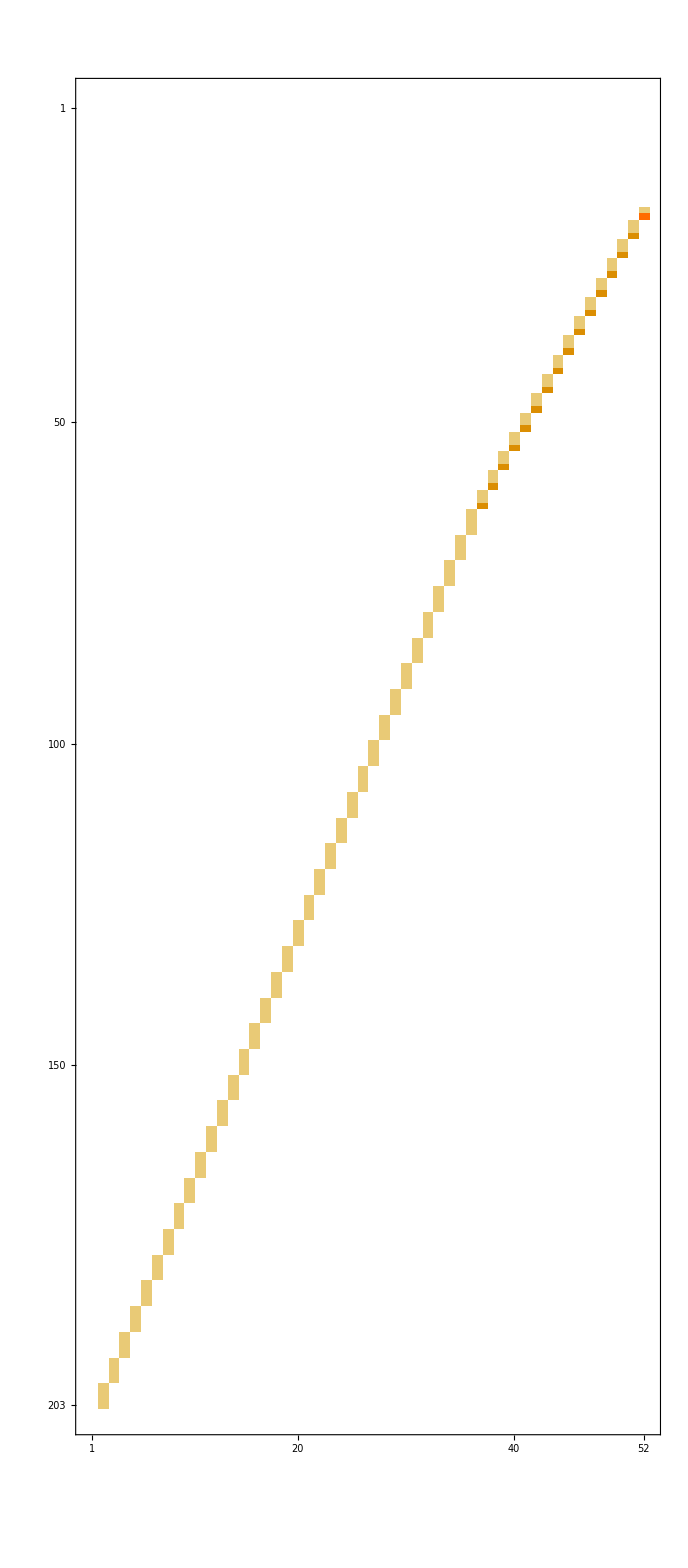

```mathematica
MatrixPlot[Sort[Table[BaseCoeffF[allGraphs6[k,"colofour"]/.repSix2Five],{k,allGraphs6AtomKeys}]/.x->4]]
```

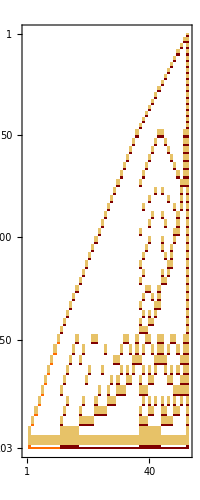

```mathematica
MatrixPlot[Sort[Table[BaseCoeffF[allGraphs6[k,"colofour"]/.repSix2Five],{k,allGraphs6NullAtomKeys}]]]/.x->4
```

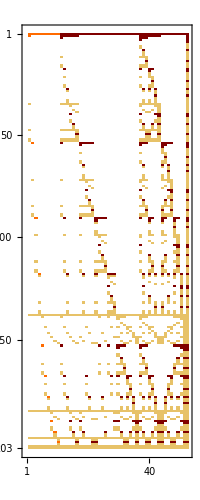

```mathematica
MatrixPlot[Table[BaseCoeffF[allGraphs6[k,"colofour"]/.repSix2Five],{k,allGraphs6NullAtomKeys}]]/.x->4
```

```mathematica
DeleteDuplicates[Sort[Table[BaseCoeffF[(allGraphs6[k,"colofour"]/.repSix2Five)/.x->4],{k,Keys[allGraphs6]}]]]//Length
```

30718

```mathematica
Length[Keys[allGraphs5]]
```

1895

```mathematica
30718/1895//N
```

16.21

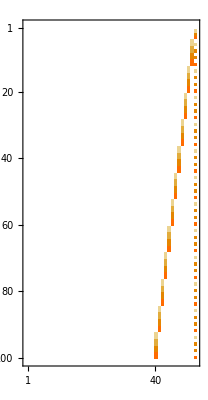

```mathematica
Take[Sort[DeleteDuplicates[Table[BaseCoeffF[(allGraphs6[k,"colofour"]/.repSix2Five)/.x->4],{k,Keys[allGraphs6]}]]],100]//MatrixPlot
```

```mathematica
MatrixRank[Table[BaseCoeffF[(allGraphs6[k,"colofour"]/.repSix2Five)/.x->4],{k,Keys[allGraphs6]}]]
```

51

```mathematica
Take[Sort[DeleteDuplicates[Table[BaseCoeffF[(allGraphs6[k,"colofour"]/.repSix2Five)/.x->4],{k,Keys[allGraphs6]}]]],{10000,10100}]//MatrixForm
```

(0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 2 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 3 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 3 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 3 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 3 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 3 | 3 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 2 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 2 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 2 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 2 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 2 | 2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 2 | 2 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 2 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 3 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 3 | 3 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 3 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 3 | 3 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 3 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 3 | 3 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 3 | 3 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 3 | 3 | 3 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 3 | 3 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 0 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 0 | 2 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 0 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 3 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 2 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 3 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 3 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 2 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 3 | 2 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 2 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 2 | 2 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)